## Hopf Fussmann - Figure with power spectra and bifurcation diagram

## Setup

```mathematica
(* Set Directory *)
SetDirectory["/Users/tb460/Library/Mobile Documents/com~apple~CloudDocs/Research/critical_transitions_18/hopf_fussmann_2000"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};

(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

## Import data

```mathematica
(* power spectrum data *)
pspecChlorRaw=Import["data_export/pspec_chlor.csv"];
pspecBrachRaw=Import["data_export/pspec_brach.csv"];
(* time-series data *)
seriesRaw=Import["data_export/series_data.csv"];
(* ews data *)
ewsChlorRaw=Import["data_export/ews_chlor.csv"];
ewsBrachRaw=Import["data_export/ews_brach.csv"];
```

### Curate data

```mathematica
deltaVals=Union[seriesRaw[[2;;,1]]];
```

```mathematica
(* time-series data *)
```

```mathematica
seriesRaw[[1]]
```

{Delta,day#,Chlorella,Brachionus}

```mathematica
seriesRaw[[1]]
```

{Delta,day#,Chlorella,Brachionus}

```mathematica
seriesChlor=Table[
Cases[seriesRaw,
{deltaVals[[i]],_,_,_}][[;;,{2,3}]],
{i,1,Length[deltaVals]}];

seriesBrach=Table[
Cases[seriesRaw,
{deltaVals[[i]],_,_,_}][[;;,{2,4}]],
{i,1,Length[deltaVals]}];
```

```mathematica
(* power spectrum data *)
pspecChlorRaw[[1]]
```

{Delta,Frequency,Empirical}

```mathematica
pspecChlor=Table[
Cases[pspecChlorRaw,
{deltaVals[[i]],_,_}][[;;,{2,3}]],
{i,1,Length[deltaVals]}];
```

```mathematica
pspecBrach=Table[
Cases[pspecBrachRaw,
{deltaVals[[i]],_,_}][[;;,{2,3}]],
{i,1,Length[deltaVals]}];
```

```mathematica
(* ews data *)
ewsChlorRaw[[1]]
```

{Delta,Variance,Coefficient of variation,Lag-1 AC,Lag-2 AC,Smax,AIC fold,AIC hopf,AIC null}

```mathematica
aicChlor=ewsChlorRaw[[2;;,{7,8,9}]];
smaxChlor=ewsChlorRaw[[2;;,6]];

aicBrach=ewsBrachRaw[[2;;,{7,8,9}]];
smaxBrach=ewsBrachRaw[[2;;,6]];
```

## Time-series figures

```mathematica
deltaVals
```

{0.04,0.07,0.12,0.32,0.64,0.67,0.69,0.89,0.95,1.,1.15,1.17,1.24,1.37}

```mathematica
index={1,4,5,9,13,14};
deltaValsFilt=deltaVals[[index]]
```

{0.04,0.32,0.64,0.95,1.24,1.37}

```mathematica
(* delta values to include *)
aRatio=0.9;
imgSize=220;
labelPos={0.5,1.15};
padding={{50,50},{50,30}};
```

### delta=0.04

```mathematica
series=seriesChlor[[index[[1]]]];
fig1Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{"Chlorella (10^6 cells/ml)",Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Automatic,None}},
FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[index[[1]]]],{3,2}]],14],Scaled[labelPos]],
Text[Style["b",14,Bold],Scaled[{0.1,0.5}]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[index[[1]]]];
fig1Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{None,None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

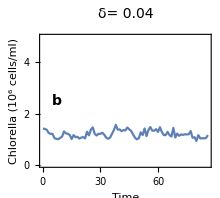
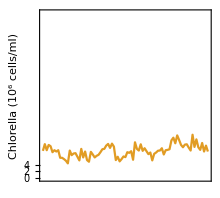

```mathematica
(* overlay the plots *)
fig1=Overlay[{fig1Chlorella,fig1Brach}]
```

### delta=0.32

```mathematica
series=seriesChlor[[index[[2]]]];
fig2Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{"Chlorella (10^6 cells/ml)",Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[index[[2]]]],{3,2}]],14],Scaled[labelPos]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[index[[2]]]];
fig2Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

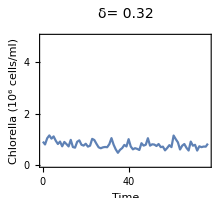
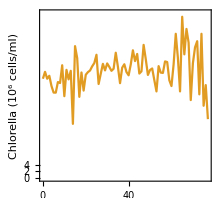

```mathematica
(* overlay the plots *)
fig2=Overlay[{fig2Chlor,fig2Brach}]
```

### delta=0.64

```mathematica
series=seriesChlor[[index[[3]]]];
fig3Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{"Chlorella (10^6 cells/ml)",Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[index[[3]]]],{3,2}]],14],Scaled[labelPos]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[index[[3]]]];
fig3Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

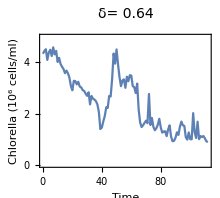
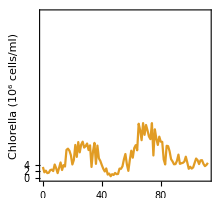

```mathematica
(* overlay the plots *)
fig3=Overlay[{fig3Chlor,fig3Brach}]
```

### delta=0.95

```mathematica
series=seriesChlor[[index[[4]]]];
fig4Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{"Chlorella (10^6 cells/ml)",Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[index[[4]]]],{3,2}]],14],Scaled[labelPos]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[index[[4]]]];
fig4Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

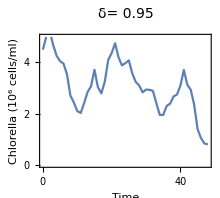
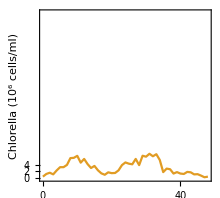

```mathematica
(* overlay the plots *)
fig4=Overlay[{fig4Chlor,fig4Brach}]
```

### delta=1.24

```mathematica
series=seriesChlor[[index[[5]]]];
fig5Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{"Chlorella (10^6 cells/ml)",Style["Brachionus (females/ml)",White]},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameTicksStyle->{{Automatic,Directive[FontOpacity->0,FontSize->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[index[[5]]]],{3,2}]],14],Scaled[labelPos]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[index[[5]]]];
fig5Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],Style["Brachionus (females/ml)",White]},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],Directive[FontOpacity->0]},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

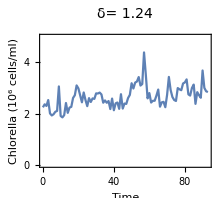
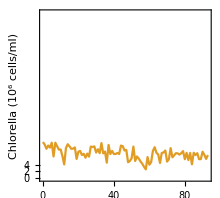

```mathematica
(* overlay the plots *)
fig5=Overlay[{fig5Chlor,fig5Brach}]
```

### delta=1.37

```mathematica
series=seriesChlor[[index[[6]]]];
fig6Chlor=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],"Brachionus (females/ml)"},{"Time",""}},
Frame->{{True,False},{True,True}},
FrameStyle->{{TMBcolours[[1]],Automatic},{Automatic,Automatic}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameTicksStyle->{{Directive[FontOpacity->0,FontSize->0],Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[1]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,5}},
Epilog->{Text[Style["δ= "<>ToString[AccountingForm[deltaVals[[index[[6]]]],{3,2}]],14],Scaled[labelPos]]},
PlotRangeClipping->False,
AspectRatio->aRatio];
```

```mathematica
(* Plot of predator (brachionus) *)
series=seriesBrach[[index[[6]]]];
fig6Brach=ListLinePlot[series,
Joined->True,
LabelStyle->14,
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],"Brachionus (females/ml)"},{"",""}},
Frame->{{False,True},{True,True}},
FrameTicks->{{Range[0,5],Range[0,50,10]},{Range[0,80,20],None}},
FrameStyle->{{Automatic,TMBcolours[[2]]},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImagePadding->padding,
ImageSize->imgSize,
PlotStyle->{TMBcolours[[2]]},
PlotRange->{{0,Max[series[[;;,1]]]},{0,50}},
AspectRatio->aRatio];
```

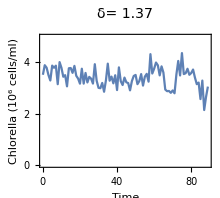
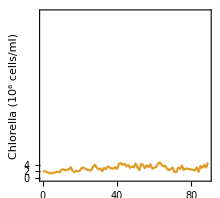

```mathematica
(* overlay the plots *)
fig6=Overlay[{fig6Chlor,fig6Brach}]
```

## Power spectrum figures

We normalise the power spectrum plots so they are on the same scale for the figure - saves using many y axes - we are just showing qualitative features of spectrum, quantiitative feature given by Smax.

```mathematica
(* plot from -wmax to wmax *)
wmax=2.7;
wTicks=Range[-2,2];
(* y axis plot range *)
yRangeChlor={0,2};
yRangeBrach={0,2};
```

### Figure 1 PSD

```mathematica
num=1;
```

```mathematica
imgpaddingPsd={{50,50},{40,20}};
imgSizePsd=220;
plotNormMax=2;

(* power spectrum data *)
psDataChlor=pspecChlor[[index[[num]]]];
psDataBrach=pspecBrach[[index[[num]]]];
```

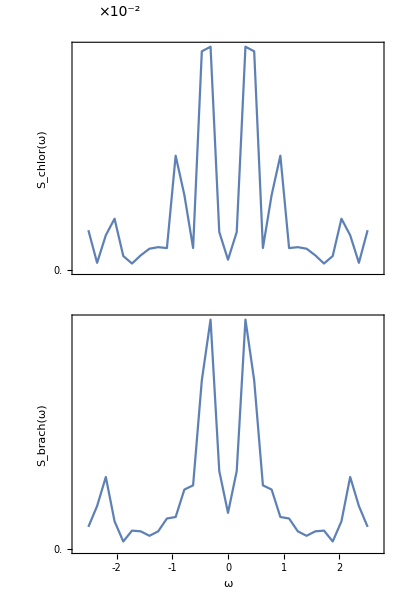

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{Transpose[{Range[0,10,0.1]*10^(-2),Range[0,10,0.1]}],None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Frame->True,
FrameTicks->{{Range[0,1.8,0.5],None},{wTicks,None}},
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

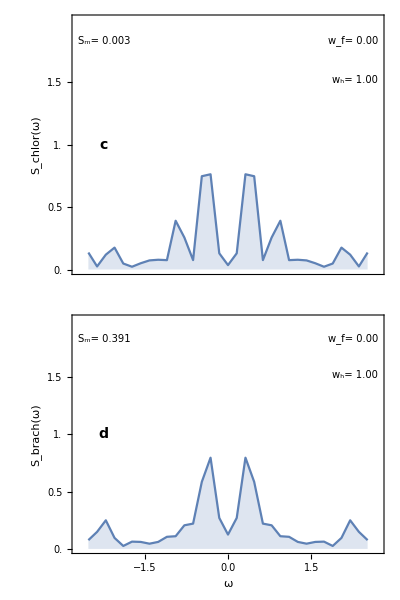

```mathematica
(* make plot for grid *)
figPsd1Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{Range[0,1.8,0.5],None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicChlor[[index[[num]],1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicChlor[[index[[num]],2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxChlor[[index[[1]]]],{3,3}]],10],Scaled[{0.02,0.9}],Left],
Text[Style["c",14,Bold],Scaled[{0.1,0.5}]]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{Range[0,1.8,0.5],None},{Automatic,None}},
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicBrach[[index[[num]],1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicBrach[[index[[num]],2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxBrach[[index[[num]]]],{3,3}]],10],Scaled[{0.02,0.9}],Left],
Text[Style["d",14,Bold],Scaled[{0.1,0.5}]]}
]}}
,Spacings->{-2,-3}]
```

### Figure 1 PSD

```mathematica
num=1;
```

```mathematica
imgpaddingPsd={{50,50},{40,20}};
imgSizePsd=220;
plotNormMax=2;

(* power spectrum data *)
psDataChlor=pspecChlor[[index[[num]]]];
psDataBrach=pspecBrach[[index[[num]]]];
```

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{Transpose[{Range[0,10,0.1]*10^(-2),Range[0,10,0.1]}],None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Frame->True,
FrameTicks->{{Range[0,1.8,0.5],None},{wTicks,None}},
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

-Graphics-

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

```mathematica
(* make plot for grid *)
figPsd1Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{Range[0,1.8,0.5],None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicChlor[[index[[num]],1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicChlor[[index[[num]],2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxChlor[[index[[1]]]],{3,3}]],10],Scaled[{0.02,0.9}],Left],
Text[Style["c",14,Bold],Scaled[{0.1,0.5}]]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{Range[0,1.8,0.5],None},{Automatic,None}},
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicBrach[[index[[num]],1]],{2,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicBrach[[index[[num]],2]],{2,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_m= "<>ToString[AccountingForm[smaxBrach[[index[[num]]]],{3,3}]],10],Scaled[{0.02,0.9}],Left],
Text[Style["d",14,Bold],Scaled[{0.1,0.5}]]}
]}}
,Spacings->{-2,-3}]
```

-Graphics-

### Figure 3 PSD

```mathematica
(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[3]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[3]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

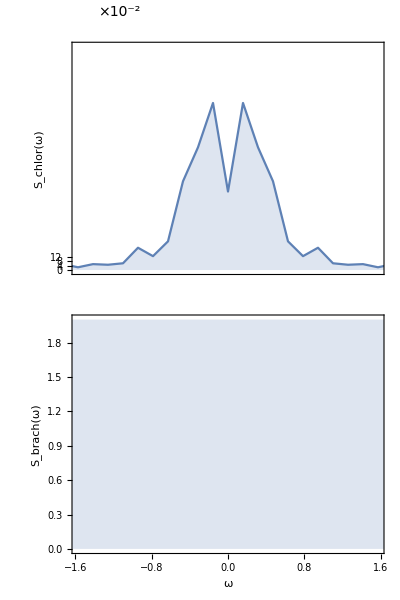

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{0.249383,26.7505}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{0.0201522,6.74747×10^-11}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{0.979848,1.}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

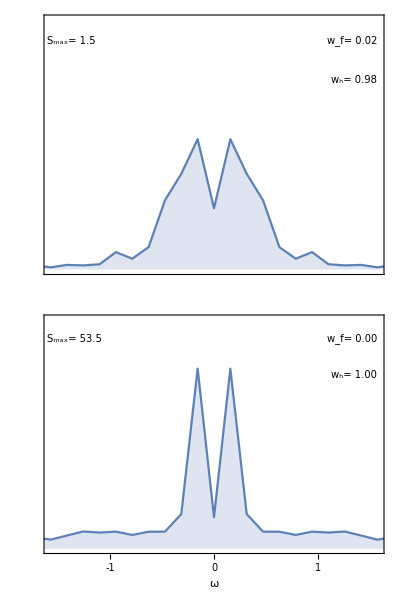

```mathematica
(* make plot for grid *)
figPsd3Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Range[-1,1],None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

### Figure 4 PSD

```mathematica
(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[4]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[4]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

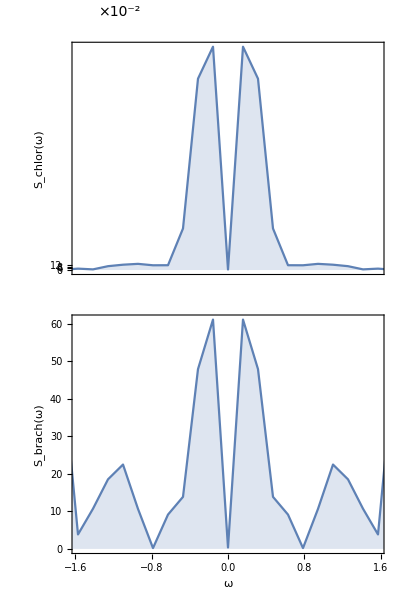

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{1.37688,15.2805}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{4.08671×10^-16,0.157733}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{1.,0.632052}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

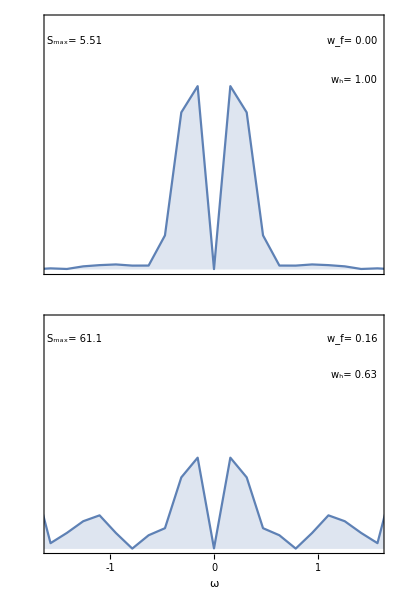

```mathematica
(* make plot for grid *)
figPsd4Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Range[-1,1],None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

### Figure 5 PSD

```mathematica
(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[5]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[5]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

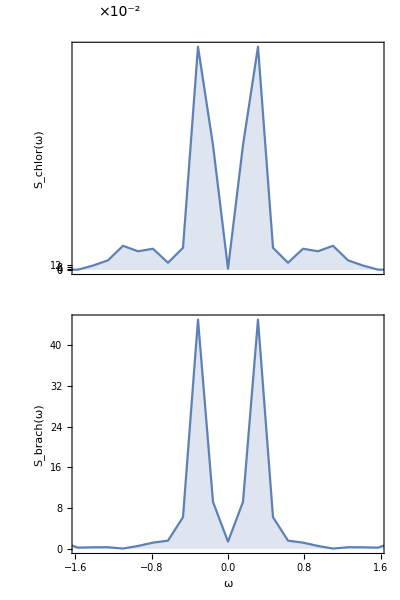

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{5.84339,45.0376}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{6.35372×10^-15,1.16729×10^-27}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{1.,1.}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

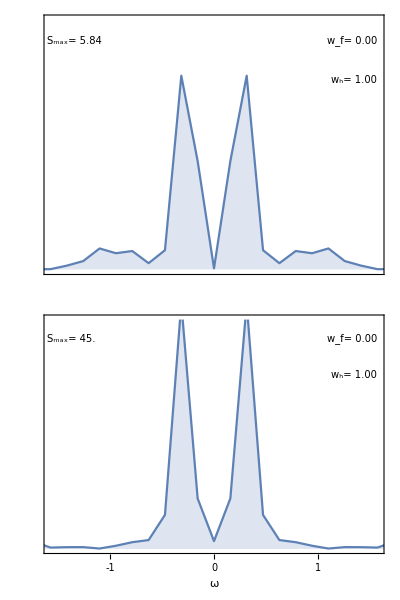

```mathematica
(* make plot for grid *)
figPsd5Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Range[-1,1],None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

### Figure 6 PSD

```mathematica
(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[6]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[6]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

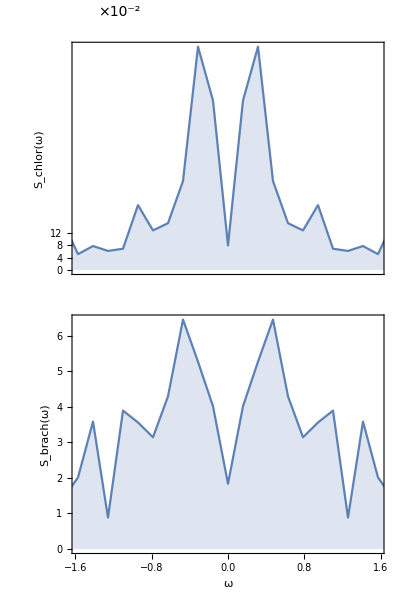

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{0.71902,4.83941}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{0.000364981,0.994791}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{0.999635,0.0000412081}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

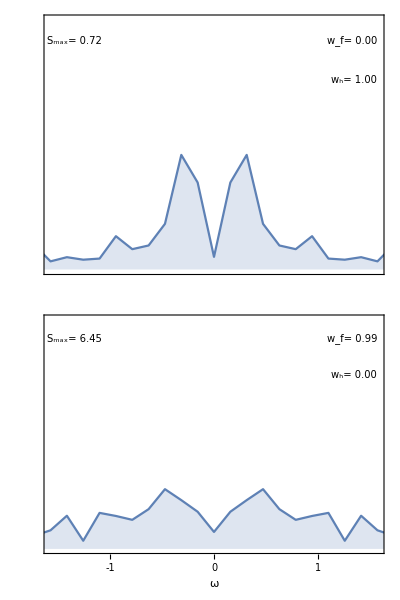

```mathematica
(* make plot for grid *)
figPsd6Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Range[-1,1],None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

### Figure 7 PSD

```mathematica
(* power spectrum data *)
psDataChlor=Transpose[psChlor[[figureNums[[7]]]]];
psDataBrach=Transpose[psBrach[[figureNums[[7]]]]];
```

```mathematica
(* compute smax for each pspec *)
smaxChlor=Max[psDataChlor[[;;,2]]];
smaxBrach=Max[psDataBrach[[;;,2]]];
```

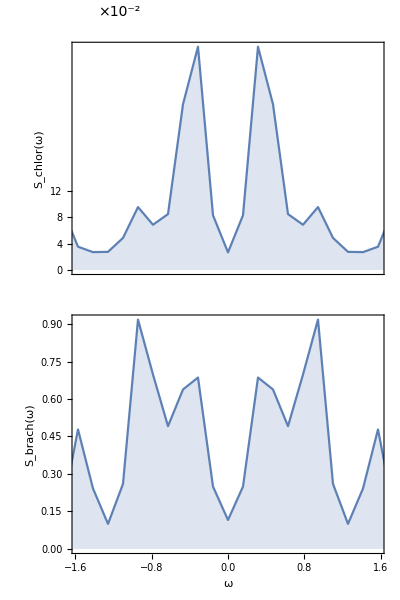

```mathematica
figPsd1=Grid[{{
ListLinePlot[psDataChlor,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"","S_chlor(ω)"},
FrameTicks->{{{{0,0},{0.04,4},{0.08,8},{0.12,12}},None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
PlotRangeClipping->False,
Epilog->Text[Style["×10^-2",14],Scaled[{0.15,1.13}]]
]},
{ListLinePlot[psDataBrach,
PlotRange->{{-wmax,wmax},All},
Filling->Bottom,
Frame->True,
FrameLabel->{"ω","S_brach(ω)"},
LabelStyle->14,
ImageSize->imgSizePsd,
PlotRangeClipping->False,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7
]}}
,Spacings->{-2,-3}]
```

```mathematica
(* coherence factor *)
{coherFactorChlor,coherFactorBrach}={TBCoherFactor[Transpose[psDataChlor]],TBCoherFactor[Transpose[psDataBrach]]}
```

{0.169145,2.75333}

```mathematica
(* fold aic weights *)
{aicFoldChlor,aicFoldBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[1]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[1]]]}
```

{6.79473×10^-7,0.098321}

```mathematica
(* hopf aic weights *)
{aicHopfChlor,aicHopfBrach}={Quiet[TBFitSpec[Transpose[psDataChlor],0.25][[2]]],Quiet[TBFitSpec[Transpose[psDataBrach],0.25][[2]]]}
```

{0.999999,0.843307}

```mathematica
(* normalise the data *)
dw=psDataChlor[[2,1]]-psDataChlor[[1,1]];
normChlor=Total[psDataChlor[[;;,2]]*dw];
psDataChlorNorm={psDataChlor[[;;,1]],psDataChlor[[;;,2]]/normChlor}//Transpose;
normBrach=Total[psDataBrach[[;;,2]]*dw];
psDataBrachNorm={psDataBrach[[;;,1]],psDataBrach[[;;,2]]/normBrach}//Transpose;
```

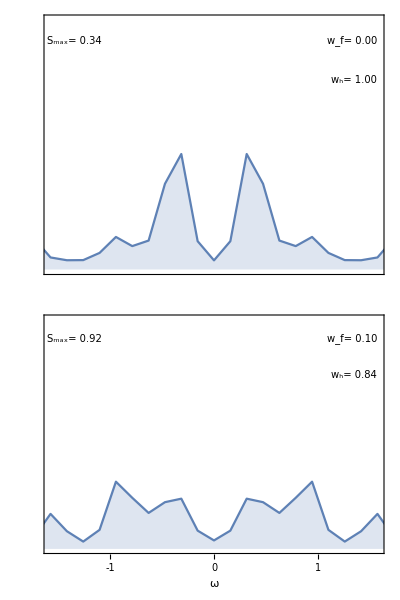

```mathematica
(* make plot for grid *)
figPsd7Norm=Grid[{{
ListLinePlot[psDataChlorNorm,
PlotRange->{{-wmax,wmax},yRangeChlor},
Filling->Bottom,
Frame->True,
FrameLabel->{"",""},
FrameTicks->{{None,None},{None,None}},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldChlor,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfChlor,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxChlor,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]},
{ListLinePlot[psDataBrachNorm,
PlotRange->{{-wmax,wmax},yRangeBrach},
Filling->Bottom,
Frame->True,
FrameTicks->{{None,None},{Range[-1,1],None}},
FrameLabel->{"ω",""},
LabelStyle->14,
ImageSize->imgSizePsd,
ImagePadding->imgpaddingPsd,
AspectRatio->0.7,
Epilog->{Text[Style["w_f= "<>ToString[AccountingForm[NumberForm[aicFoldBrach,{3,2}]]],10],Scaled[{0.98,0.9}],Right],
Text[Style["w_h= "<>ToString[AccountingForm[NumberForm[aicHopfBrach,{3,2}]]],10],Scaled[{0.98,0.75}],Right],
Text[Style["S_max= "<>ToString[AccountingForm[smaxBrach,{3,2}]],10],Scaled[{0.01,0.9}],Left]}
]}}
,Spacings->{-2,-3}]
```

## Bifurcation diagram

### Import Bifurcation Data

```mathematica
bifPtsChlor=Import["data/bifPtsChlor.mat"];
bifPtsBrach=Import["data/bifPtsBrach.mat"];
```

```mathematica
figureNums={1,4,5,9,13,14};
```

```mathematica
(* remove delta value of time-series that are too short for EWS *)

deltaValsSelect=deltaVals[[figureNums]];
```

```mathematica
(* mark on approximate bifurcation points from experiment *)
expBif1a=deltaValsShort[[4]];
expBif1b=deltaValsShort[[5]];
expBif2=deltaValsShort[[9]];
expBifPts={expBif1a,expBif1b,expBif2};
```

```mathematica
(* figure params *)
colChlor=TMBcolours[[1]];
colBrach=TMBcolours[[2]];
lt=0.004;
ltExt=0.0012;
imgs=900;
aRatio=0.22;
padding={{50,50},{30,50}};
```

### Bif Figure Code

```mathematica
(* chlorella bif *)
bifPlotChlor=ListLinePlot[bifPtsChlor,
PlotStyle->Table[{colChlor,Thickness[lt]},{i,1,Length[bifPtsChlor]}],
LabelStyle->14,
InterpolationOrder->1,
PlotRange->{{0,1.5},{0,4.2}*1000000},
Frame->{{True,False},{True,True}},
FrameLabel->{{"Chlorella (10^6 cells/ml)",Style["Brachionus (females/ml)",White]},{"","Dilution rate δ (per day)"}},
FrameTicks->{{Transpose[{Range[-4/40,4]*1000000,Range[0,4]}],None},{Automatic,Range[0,2,0.2]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameStyle->{{colChlor,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
PlotRangeClipping->False,
ImagePadding->padding,
Epilog->{EdgeForm[Directive[Black,Thickness[0]]],Opacity[0.05],Directive[Black],Rectangle[{expBif1a,0},{expBif1b,4200000}],
Rectangle[{expBif2-0.01,0},{expBif2+0.01,4200000}],
Opacity[1],
Directive[{Black,Thickness[1.5*ltExt]}],Line[Table[{Scaled[{0,-0.05},{deltaValsSelect[[i]],0}],
Scaled[{0,0.05},{deltaValsSelect[[i]],0}]},{i,1,Length[deltaValsSelect]}]],
Directive[{Black}],Text[Style["a",14,Bold],Scaled[{0.02,0.5}]]}];
```

```mathematica
(* brachionus bif *)
bifPlotBrach=ListLinePlot[bifPtsBrach,
PlotRange->{{0,1.5},{-59/40,59}},
PlotStyle->Table[{colBrach,Thickness[lt]},{i,1,Length[bifPtsBrach]}],
LabelStyle->14,
InterpolationOrder->1,
Frame->{{False,True},{True,True}},
FrameLabel->{{Style["Chlorella (10^6 cells/ml)",White],"Brachionus (females/ml)"},{"",""}},
FrameTicks->{{None,Range[0,60,10]},{None,None}},
FrameStyle->{{Automatic,colBrach},{Automatic,Automatic}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
ImageSize->imgs,
AspectRatio->aRatio,
PlotRangeClipping->False,
ImagePadding->padding];
```

### Bif Output

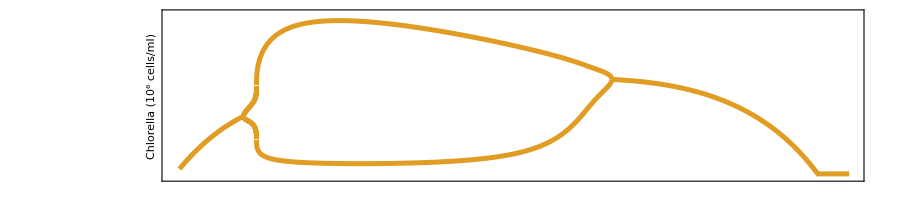
-Graphics--Graphics-

```mathematica
(* put together *)
bifPlot=Overlay[{bifPlotChlor,bifPlotBrach}]
```

## Bring it all together

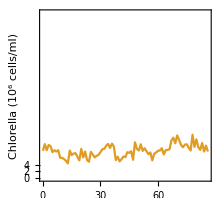
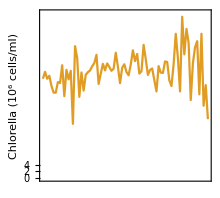
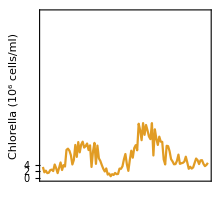
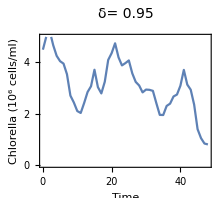
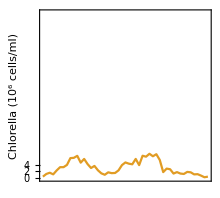
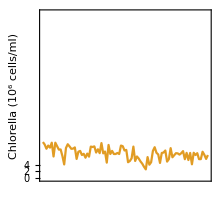
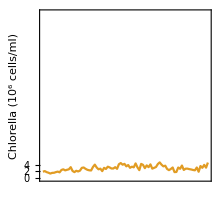
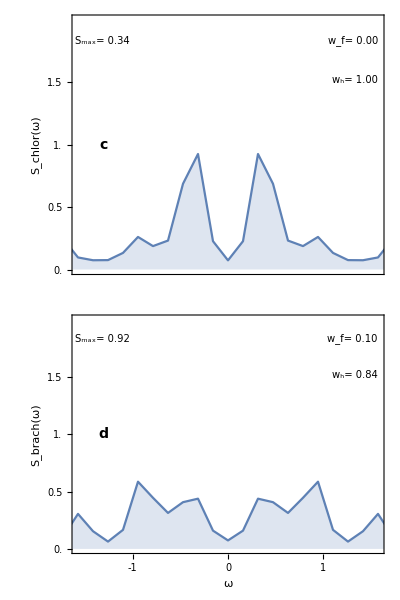
-Graphics--Graphics- |  |  |  |  | 
-Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics- | -Graphics--Graphics-
-Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics- | -Graphics-

```mathematica
gridFussmann=Grid[{{bifPlot,SpanFromLeft},{fig1,fig2,fig3,fig5,fig6,fig7},{figPsd1Norm,figPsd2Norm,figPsd3Norm,figPsd5Norm,figPsd6Norm,figPsd7Norm}},Spacings->{-6.5,0}]
```

The fact that the bifurcation diagram doesn’t line up with the real data just goes to confirm that we cannot predict bifurcations from models alone - require help from generic early warning signals.

```mathematica
Export["figures/fussmann_ews_pspecs.png",gridFussmann,ImageResolution->200];
```